https://www.wolframphysics.org/technical-introduction/the-updating-process-for-string-substitution-systems/causal-foliations-and-causal-cones/index.html
https://resources.wolframcloud.com/FunctionRepository/resources/SubstitutionSystemCausalEvolution/?i=SubstitutionSystemCausalEvolution&searchapi=https%3A%2F%2Fresources.wolframcloud.com%2FFunctionRepository%2Fsearch

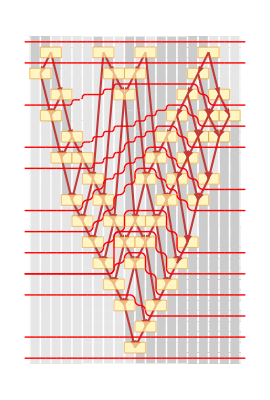

```mathematica
CloudGet["https://wolfr.am/LhaceyND"];
evo=(SeedRandom[2424];
ResourceFunction["SubstitutionSystemCausalEvolution"][{"BA"->"AB"},"BBAAAABAABBABBBBBAAA",15,{"Random",4}]);
With[{evoSequential=ResourceFunction["SubstitutionSystemCausalEvolution"][{"BA"->"AB"},"BBAAAABAABBABBBBBAAA",12]},ResourceFunction["SubstitutionSystemCausalPlot"][evo,EventLabels->False,CellLabels->False,CausalGraph->True,SpaceSurfaceStyle->Directive[Red,Thick],PlotSpaceSurfaces->((FoldList[Join[#,#2]&,{},TakeList[Range[Total[#]],#]&@(Length/@Rest[evoSequential][[All,2]])])/. (FindGraphIsomorphism@@causalGraph/@elementTransitionGraph/@{evoSequential,evo})[[1]])]]
```